## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/a-w/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/a-w

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 21.9133 | 0.215001
1000. | 0. | 46.8115 | 0.309579
2000. | 0. | 95.8218 | 0.41752
3000. | 0. | 144.99 | 0.534319
4000. | 0. | 193.475 | 0.664827
5000. | 0. | 242.151 | 0.717067
6000. | 0. | 290.413 | 0.777219
7000. | 0. | 337.612 | 0.84899
8000. | 0. | 387.085 | 0.88083
9000. | 0. | 439.342 | 0.816248
10000. | 0. | 482.716 | 0.935875

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-2.2914+0.0490675 x-4.07809×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.2914 | 1.23123 | -1.86107 | 0.0997663
x | 0.0490675 | 0.000569777 | 86.1171 | 3.68823×10^-13
x^2 | -4.07809×10^-8 | 5.37134×10^-8 | -0.759231 | 0.469492

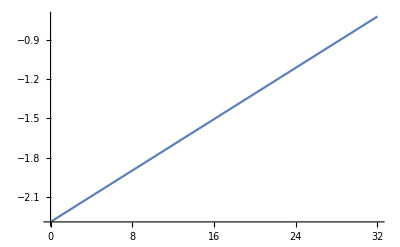

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{-0.318859,0.0761994,0.141308,0.445924,0.148771,0.124137,-0.232739,-1.57115,-0.55331,3.32916,-1.58944}

{0.215001,0.309579,0.41752,0.534319,0.664827,0.717067,0.777219,0.84899,0.88083,0.816248,0.935875}

{2.19946,0.0605841,0.114546,0.6965,0.0500749,0.0299699,0.0896711,3.42478,0.394595,16.6351,2.88437}

3.32245

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

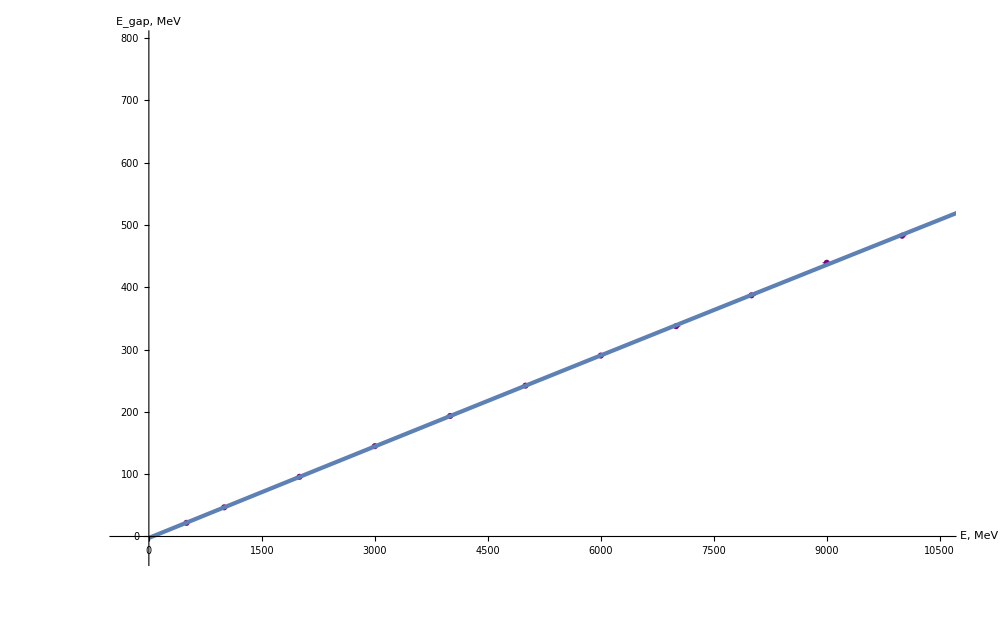

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,795}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-2.2914,0.0490675,-4.07809×10^-8},{1.23123,0.000569777,5.37134×10^-8},3.32245}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
876.836 | 7.6735 | 0.211091 | 0.00433378
1364.4 | 9.33349 | 0.17011 | 0.00334385
1936.87 | 11.1838 | 0.144685 | 0.00279392
2951.59 | 14.1871 | 0.117297 | 0.00221659
3527.01 | 15.2618 | 0.108537 | 0.00204218
4128. | 16.4305 | 0.099591 | 0.00186319
4984.08 | 19.2358 | 0.092731 | 0.00173224
6283.99 | 21.2755 | 0.0849924 | 0.00157927
7166.38 | 23.1207 | 0.0786606 | 0.00145839
8087.59 | 22.0062 | 0.0751356 | 0.00138978
9738.88 | 24.7398 | 0.0679463 | 0.00125247

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00748688+6.01597/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00748688 | 0.000725038 | 10.3262 | 2.73756×10^-6
1/(√x) | 6.01597 | 0.0381172 | 157.828 | 8.36686×10^-17

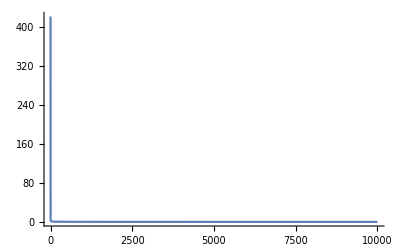

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{0.000439744,-0.000245017,0.000501711,-0.000923399,-0.000247866,-0.00153037,0.0000296563,0.00161493,0.000108751,0.000753364,-0.000501506}

{0.00433378,0.00334385,0.00279392,0.00221659,0.00204218,0.00186319,0.00173224,0.00157927,0.00145839,0.00138978,0.00125247}

{0.0102959,0.00536905,0.0322462,0.173543,0.0147315,0.674648,0.0002931,1.04567,0.00556058,0.293844,0.160331}

0.268503

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

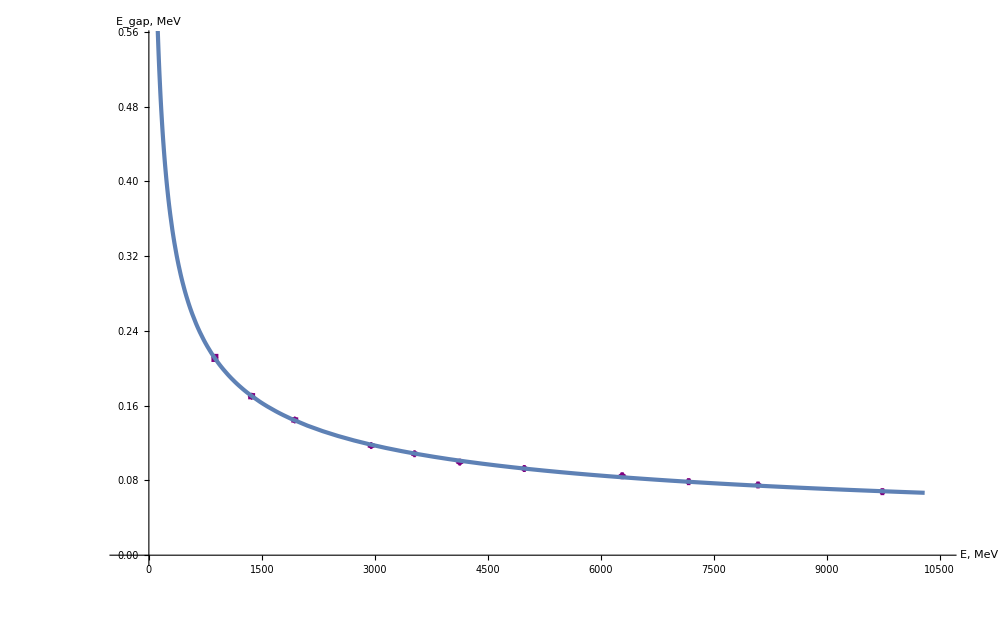

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00748688,6.01597},{0.000725038,0.0381172},0.268503}

fit_re_res.csv